InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {360} lies outside the range of data in the interpolating function. Extrapolation will be used.

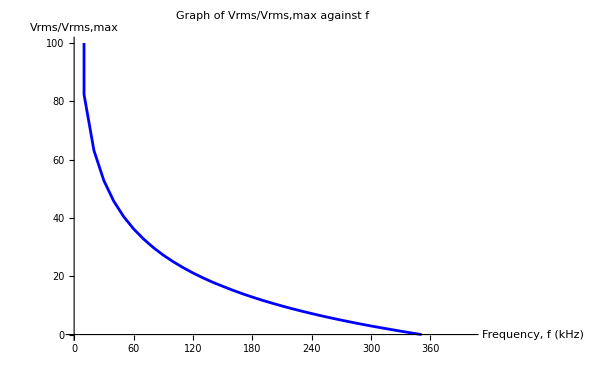
-Graphics-{81, 29.5609}, {79.3, 30.0278}, {77.1, 30.6506}, {74.6, 31.3887}, {72.2, 32.1225}, {70, 32.8084}, {67.8, 33.5275}, {65.7, 34.2382}, {63.4, 35.0348}, {62.4, 35.3862}, {60.3, 36.1489}, {58.3, 36.9202}, {58, 37.0407}, {56.8, 37.5373}, {56, 37.8735}, {54.6, 38.4556}, {53.4, 38.9577}, {52.6, 39.2972}, {51.2, 39.9099}, {51.2, 39.9099}, {51.9, 39.5999}, {52.6, 39.2972}, {53.2, 39.0422}, {53.8, 38.7894}, {54.3, 38.5804}, {54.9, 38.3311}, {55.5, 38.0827}, {56.1, 37.8314}, {56.6, 37.6211}, {57.2, 37.3704}, {57.7, 37.1636}, {58.2, 36.96}, {58.6, 36.8015}, {59.1, 36.6061}, {59.6, 36.4136}, {60.1, 36.224}, {60.6, 36.0371}, {61, 35.8898}, {61.5, 35.7081}, {62, 35.5285}, {62.5, 35.3508}, {62.8, 35.245}, {63.3, 35.0697}, {63.7, 34.9299}, {64.1, 34.7902}, {64.5, 34.6512}, {64.9, 34.5129}, {65.4, 34.3409}, {65.8, 34.2041}, {66.2, 34.0679}, {66.6, 33.932}, {66.9, 33.8302}, {67.3, 33.6952}, {67.6, 33.5944}, {68, 33.4607}, {68.4, 33.3279}, {68.8, 33.196}, {69.2, 33.0651}, {69.5, 32.9679}

```mathematica
data={{351,0},{332.6,1},{315.6,2},{299,3},{283.6,4},{269.1,5},{255.4,6},{242.5,7},{230.3,8},{218.7,9},{207.9,10},{197.6,11},{187.8,12},{178.7,13},{170,14},{161.7,15},{154.6,16},{146.6,17},{139.6,18},{133,19},{126.7,20},{120.8,21},{115.2,22},{109.9,23},{104.8,24},{100,25},{95.5,26},{91.1,27},{87,28},{83.1,29},{79.4,30},{75.9,31},{72.6,32},{69.4,33},{66.4,34},{63.5,35},{60.7,36},{58.1,37},{55.7,38},{53.3,39},{51,40},{48.9,41},{46.9,42},{44.9,43},{43.1,44},{41.3,45},{39.6,46},{38,47},{36.5,48},{35,49},{33.6,50},{32.3,51},{31,52},{29.8,53},{28.6,54},{27.5,55},{26.4,56},{25.4,57},{24.4,58},{23.5,59},{22.6,60},{21.7,61},{20.9,62},{20.1,63},{19.4,64},{18.7,65},{18,66},{17.3,67},{16.7,68},{16.1,69},{15.5,70},{14.9,71},{14.4,72},{13.9,73},{13.4,74},{12.9,75},{12.5,76},{12,77},{11.6,78},{11.2,79},{10.8,80},{10.5,81},{10.1,82},{9.8,83},{9.4,84},{9.1,85},{8.8,86},{8.5,87},{8.2,88},{8,89},{7.7,90},{7.5,91},{7.2,92},{7,93},{6.8,94},{6.5,95},{6.3,96},{6.1,97},{5.9,98},{5.7,99},{5.6,100}};

smoothCurve=Interpolation[data];

(*Define a function to find y-values for a given list of x-values*)
findPointsOnCurve[x_List]:=Table[{xi,smoothCurve[xi]},{xi,x}];

(*List of x-values*)
xValues={81,79.3,77.1,74.6,72.2,70,67.8,65.7,63.4,62.4,60.3,58.3,58,56.8,56,54.6,53.4,52.6,51.2,51.2,51.9,52.6,53.2,53.8,54.3,54.9,55.5,56.1,56.6,57.2,57.7,58.2,58.6,59.1,59.6,60.1,60.6,61,61.5,62,62.5,62.8,63.3,63.7,64.1,64.5,64.9,65.4,65.8,66.2,66.6,66.9,67.3,67.6,68,68.4,68.8,69.2,69.5};  (*Customize this list as needed*)
points=findPointsOnCurve[xValues];

(*Convert the points list to a string*)
pointsString=StringJoin[Riffle[ToString/@points,", "]];

(*Create the plot*)
plot=ListLinePlot[Table[{x,smoothCurve[x]},{x,0,360,10}],PlotStyle->Blue,AxesLabel->{"Frequency, f (kHz)","Vrms/Vrms,max"},PlotLabel->"Graph of Vrms/Vrms,max against f",PlotRange->{{0,400},{0,100}},Ticks->{{#,NumberForm[#,{3,1}]}&/@Range[0,360,20],{#,NumberForm[#,{3,1}]}&/@Range[0,100,20]}];

(*Attach the list of points as a label below the plot*)
Labeled[plot,Style[pointsString,Small],Bottom]
```